```mathematica
Clear["Global`*"]
```

WIKIPEDIA

```mathematica
tend=50;
eq={x'[t]==σ (y[t]-x[t]),y'[t]==x[t] (ρ-z[t])-y[t],z'[t]==x[t] y[t]-β z[t]};
init={x[0]==10,y[0]==10,z[0]==10};
pars={σ->10,ρ->28,β->8/3};
{xs,ys,zs}=NDSolveValue[{eq/. pars,init},{x,y,z},{t,0,tend}];
ParametricPlot3D[{xs[t],ys[t],zs[t]},{t,0,tend}]
```

-Graphics3D-

```mathematica
lorenz=NonlinearStateSpaceModel[{{σ (y-x),x (ρ-z)-y,x y-β z},{}},{x,y,z},{σ,ρ,β}];
soln[t_]=StateResponse[{lorenz,{10,10,10}},{10,28,8/3},{t,0,50}];
ParametricPlot3D[soln[t],{t,0,50}]
```

-Graphics3D-

```mathematica
eqs={x'[t]==σ (y[t]-x[t]),y'[t]==x[t] (ρ-z[t])-y[t],z'[t]==x[t] y[t]-β z[t],x[0]==10,y[0]==10,z[0]==10};
tmax=50;
sol=ParametricNDSolveValue[eqs,Function[t,{x[t],y[t],z[t]}],{t,0,tmax},{σ,ρ,β}];
Manipulate[fun=sol[σ,ρ,β];
plot=ParametricPlot3D[fun[t],{t,0,tmax},PlotRange->All,PerformanceGoal->"Quality"];
Animate[Show[plot,Graphics3D[{PointSize[0.05],Red,Point[fun[t]]}]],{t,0,tmax},AnimationRunning->True,AnimationRate->1],{{σ,10},0,100},{{ρ,28},0,100},{{β,8/3},0,100},TrackedSymbols:>{σ,ρ,β}]
```

Visualization`Core`ParametricPlot3D::plln: Limiting value tmax in {t,0,tmax} is not a machine-sized real number.

Animate::vsform: Animate argument {t,0,tmax} does not have the correct form for a variable specification.

General::stop: Further output of Animate::vsform will be suppressed during this calculation.

Visualization`Core`ParametricPlot3D::plln: Limiting value tmax in {t,0,tmax} is not a machine-sized real number.

Animate::vsform: Animate argument {t,0,tmax} does not have the correct form for a variable specification.

General::stop: Further output of Animate::vsform will be suppressed during this calculation.

1) Stationary points

```mathematica
Solve[0==σ (y-x) && 0==x (r-z)-y && 0==x y-b z,{x,y,z}] //TableForm
```

x→0 | y→0 | z→0
x→-√b √(-1+r) | y→-√b √(-1+r) | z→-1+r
x→√b √(-1+r) | y→√b √(-1+r) | z→-1+r

2) r<1 -> origin attracts all trajectories

```mathematica
x'[t]=σ (y[t]-x[t]);
y'[t]=x[t] (r-z[t])-y[t];
z'[t]=x[t]*y[t]-z[t];
```

b = 1 and σ > b+1 and if r<1

```mathematica
D[x[t]^2+σ*y[t]^2+σ*z[t]^2,t]  //FullSimplify
```

-2 σ (x[t]^2-(1+r) x[t] y[t]+y[t]^2+z[t]^2)

```mathematica
Ljap[σ_]:=x[t]^2+σ*y[t]^2+σ*z[t]^2;
```

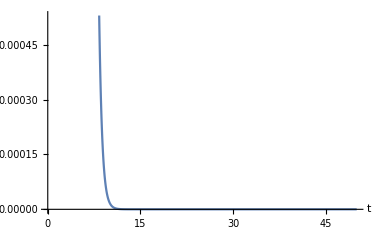

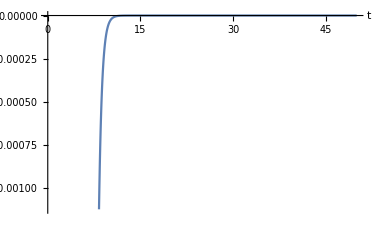

```mathematica
t2=50;
σ=50;
r = -3;
res[σ_,ρ_,β_]:=NDSolve[{x'[t]==σ (y[t]-x[t]),y'[t]==x[t] (ρ-z[t])-y[t],z'[t]==x[t] y[t]-β z[t],x[0]==10,y[0]==10,z[0]==10},{x[t],y[t],z[t]},{t,0,t2}];
Plot[Evaluate[Ljap[σ]/.res[σ,r,1]],{t,0,t2},AxesLabel -> Automatic]
Plot[Evaluate[-2 σ (x[t]^2-(1+r) x[t] y[t]+y[t]^2+z[t]^2)/.res[σ,r,1]],{t,0,t2},AxesLabel -> Automatic]
```

```mathematica
tabb=Table[Evaluate[-2 σ (x[t]^2-(1+r) x[t] y[t]+y[t]^2+z[t]^2)/.res[σ,r,1]], {t,0.01, 10,0.5}]
```

{{-45103.},{-6460.2},{-2376.57},{-874.292},{-321.634},{-118.323},{-43.5285},{-16.0132},{-5.89093},{-2.16715},{-0.797251},{-0.293292},{-0.107896},{-0.0396928},{-0.0146022},{-0.00537189},{-0.00197622},{-0.000727016},{-0.000267458},{-0.0000983946}}